# Analysis of Packing V3E05L0N01T2_1

Three Vertices, Five Edges, 0 Loops,Combinatorial Number 01, Face Pattern 2, Type 1

```mathematica
-Graphics-;
```

These are the x and y coordinates in terms of β and α.  The coordinates come from realizing that 2 is on the perpendicular bisector  of w1.  Similarly, 3 is on the perpendicular bisector of w1, plus w2.  That is exactly what we have; we take the angle -α and then simply add w2.   Note that we are scaling such that the side length of the big circle is 1/2.  Also note that L is the magnitude of vector w2.

```mathematica
x2:=(1/Sqrt[2])*Cos[α]
```

```mathematica
y2:=(1/Sqrt[2])*Sin[α]
```

```mathematica
x3:=(1/Sqrt[2])*Cos[-α]+L*Cos[β+α]
```

```mathematica
y3:=(1/Sqrt[2])*Sin[-α]+L*Sin[β+α]
```

Now, we have used all the information regarding tangencies, except for the fact that the two small circles are tangent.  We can use the distance formula and solve for L.

```mathematica
FullSimplify[Solve[(x3-x2)^2+(y3-y2)^2==(Sqrt[2]-1)^2,L]]
```

{{L→-1/2 √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)])+√2 Sin[α] Sin[α+β]},{L→1/2 √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)])+√2 Sin[α] Sin[α+β]}}

```mathematica
N[1/2 √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)])+√2 Sin[α] Sin[α+β]/.{α->Pi/4,β->Pi/4}]
```

1.41421

Numerically check to see which one is positive because L cannot be negative.

```mathematica
Simplify[x3/.L-> 1/2 √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)])+√2 Sin[α] Sin[α+β]]
```

Cos[α]/(√2)+1/2 Cos[α+β] (√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)])+2 √2 Sin[α] Sin[α+β])

```mathematica
Simplify[y3/.L-> 1/2 √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)])+√2 Sin[α] Sin[α+β]]
```

1/2 (-√2 Cos[2 (α+β)] Sin[α]+√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]) Sin[α+β])

```mathematica
Simplify[L*Cos[β+α]/.L-> 1/2 √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)])+√2 Sin[α] Sin[α+β]]
```

1/2 Cos[α+β] (√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)])+2 √2 Sin[α] Sin[α+β])

```mathematica
Simplify[L*Sin[β+α]/.L-> 1/2 √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)])+√2 Sin[α] Sin[α+β]]
```

1/2 Sin[α+β] (√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)])+2 √2 Sin[α] Sin[α+β])

Here we substitute in for L into our original circle centers.  Thus, we now have the centers in terms of two varibles.

We also want to prevent any of circles being able to “pop out”, i.e. we don’t want any of the tangencies of the small circles to be contained in a semi circle.  Slope C2C3 is the slope between the two small circles; similarly the slope between C1C2 is between the big circle and C2 (the small circle).

```mathematica
slopeC2C3 := FullSimplify[(y3-y2)/(x3-x2)/.L-> 1/2 √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)])+√2 Sin[α] Sin[α+β]]
slopeC2C3
```

(-2 √2 Cos[α+β] Sin[α]+√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]) Tan[α+β])/(√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)])+2 √2 Sin[α] Sin[α+β])

```mathematica
slopeC1C2 := FullSimplify[(0-y2)/(0-x2)/.L-> 1/2 √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)])+√2 Sin[α] Sin[α+β]]
slopeC1C2
```

Tan[α]

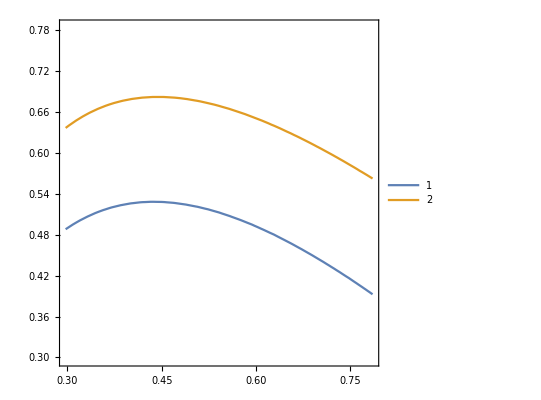

```mathematica
ContourPlot[{slopeC2C3==0,slopeC2C3==slopeC1C2},{α,ArcSin[1-1/(√2)],Pi/4},{β,ArcSin[1-1/(√2)],Pi/4},PlotLegends->Automatic]
```

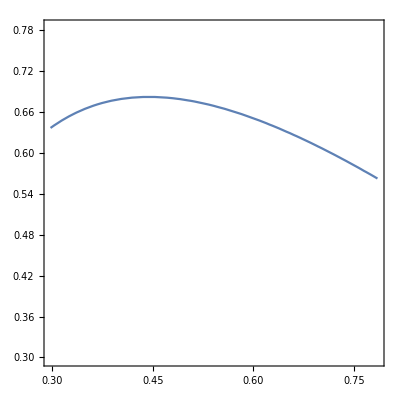

```mathematica
ContourPlot[slopeC2C3==slopeC1C2,{α,ArcSin[1-1/(√2)],Pi/4},{β,ArcSin[1-1/(√2)],Pi/4}]
```

## Circle Centers and Radii

```mathematica
centers = {{0,0},{(1/Sqrt[2])*Cos[α],(1/Sqrt[2])*Sin[α]},{Cos[α]/(√2)+1/2 Cos[α+β] (√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)])+2 √2 Sin[α] Sin[α+β]),1/2 (-√2 Cos[2 (α+β)] Sin[α]+√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]) Sin[α+β])}
}
```

{{0,0},{Cos[α]/(√2),Sin[α]/(√2)},{Cos[α]/(√2)+1/2 Cos[α+β] (√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)])+2 √2 Sin[α] Sin[α+β]),1/2 (-√2 Cos[2 (α+β)] Sin[α]+√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]) Sin[α+β])}}

## Lattice Vectors

W2 comes from simply taking (L*Cos[α+β], L*Sin[α+β]) and substituting in our value of L.

We are working this flat torus

```mathematica
latticeVectors = {
 {(2/Sqrt[2])*Cos[α],0},
{ 1/2 Cos[α+β] (√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)])+2 √2 Sin[α] Sin[α+β]),1/2 Sin[α+β] (√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)])+2 √2 Sin[α] Sin[α+β])}};
```

Need length of w2 to be greater than 1 to prevent overlap

```mathematica
Simplify[Sqrt[(1/2 Cos[α+β] (√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)])+2 √2 Sin[α] Sin[α+β]))^2+(1/2 Sin[α+β] (√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)])+2 √2 Sin[α] Sin[α+β]))^2]]
```

1/2 √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]+4 √2 √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]) Sin[α] Sin[α+β]+8 Sin[α]^2 Sin[α+β]^2)

## Edges

Here we store the edges a list {i,j,m,n} where center[[i]] is connected to center[[j]] + m*latticeVectors[[1]] + n*latticeVectors[2]]
center[[i]] is *always* in the fundamental domain ****the last two numbers are winding numbers****

```mathematica
edges = {{1,2,0,0},{2,3,0,0},{2,1,1,0},{3,1,0,1},{3,1,1,1}};
```

### Check the edge lengths are all 2rs= Sqrt[2]-1 or rs+rb=Sqrt[2]rb=Sqrt[2]/2=1/Sqrt[2]

```mathematica
For[i=1,i≤Length[edges],i++,
P1:= centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]];
P2:= centers[[edges[[i,1]] ]];
Print["Edge ",i,": Length is ",
Sqrt[FullSimplify[(P1[[1]]-P2[[1]])^2+(P1[[2]]-P2[[2]])^2,{0≤α≤ Pi/2,Pi/3≤α+β≤Pi/2,0≤β≤ Pi/2}]]];
]
```

Edge 1: Length is 1/(√2)

Edge 2: Length is √(3-2 √2)

Edge 3: Length is 1/(√2)

Edge 4: Length is 1/(√2)

Edge 5: Length is 1/(√2)

Yes!

## Packing Visualization

Here we visualize the packing and the fundamental domain to help determine the value of the parameters for which this is a packing graph.

```mathematica
Manipulate[
Graphics[
Translate[
Union[
Table[{Thick,Dashing[1],Black,Line[{centers[[edges[[i,1]] ]],centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]]}/.{α->a,β->b}]},{i,1,Length[edges]}],(*Edges*)
{{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[1]]/.{α->a,β->b} }]},{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[2]]/.{α->a,β->b}}]}},(*Fundamental Domain*)
{{AbsolutePointSize[5],Point[centers/.{α->a,β->b}]}},(*Circle Centers*)
Table[Text[Style[i,Medium],centers[[i]]/.{α->a,β->b},Offset[{10,-30},{0,0}]],{i,1,Length[centers]}],(*Label Circle Centers*)
{{Opacity[.5],EdgeForm[Thick],LightOrange,Disk[centers[[1]]/.{α->a,β->b},1/2]},
{Opacity[.5],EdgeForm[Thick],LightGreen,Disk[centers[[2]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]},
{Opacity[.5],EdgeForm[Thick],LightRed,Disk[centers[[3]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]}}, (*Circles*){{Text[Style["α",Small],centers[[1]]/.{α->a,β->b},Offset[{-20,-20},{0,0}]]},
{Text[Style["β",Small],centers[[1]]/.{α->a,β->b},Offset[{0,-20},{0,0}]]}}(*Angle Markers Labels*)

], Flatten[Table[i*latticeVectors[[1]]+j*latticeVectors[[2]],{i,-2,2,1},{j,-2,2,1}]/.{α->a,β->b},1] (*List of the translation vectors*)
],PlotRange-> {{-1,3},{-1,3}} (*Restrict the plot window*)
],{{a,Pi/4,"α"},ArcSin[1-1/(√2)],Pi/4},{{b,Pi/4,"β"},1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-a,(Pi-1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))]))-a}
]
```

## Locally Maximally Dense

We have to determine for which values of α and β the packing is locally maximally dense. To be locally maximally dense (Following Connelly, Rigid Circle and Sphere Packings, Page 51, Theorem 6.1)
	1. The packing graph is rigid as a bar framework
	2. Have a proper stress that is non-zero on every member

### Rigid as bar framework

To be rigid as a bar framework we need to establish a rigid ordering of the circles. The numbering of the circles in the picture above is a rigid ordering of the packing disks -- See Lemma 6.2 in the Connelly paper on Rigid Sphere and Circle Packings. Note: The first is held fixed.

### Proper Stress

Assign a scalar to each edge of the packing and collect those scalars in a vector called ω. We need to solve the linear algebra problem where the sum of the ω_i times the vector from vertex j is zero.

```mathematica
Manipulate[
Graphics[
Translate[
Union[
Table[{Thick,Dashing[1],Black,Line[{centers[[edges[[i,1]] ]],centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]]}/.{α->a,β->b}]},{i,1,Length[edges]}],(*Edges*)
{{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[1]]/.{α->a,β->b} }]},{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[2]]/.{α->a,β->b}}]}},(*Fundamental Domain*)
{{AbsolutePointSize[5],Point[centers/.{α->a,β->b}]}},(*Circle Centers*)
Table[Text[Style[i,Medium],centers[[i]]/.{α->a,β->b},Offset[{10,-30},{0,0}]],{i,1,Length[centers]}],(*Label Circle Centers*)
{{Opacity[.5],EdgeForm[Thick],LightOrange,Disk[centers[[1]]/.{α->a,β->b},1/2]},
{Opacity[.5],EdgeForm[Thick],LightGreen,Disk[centers[[2]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]},
{Opacity[.5],EdgeForm[Thick],LightRed,Disk[centers[[3]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]}}, (*Circles*){{Text[Style["α",Small],centers[[2]]/.{α->a,β->b},Offset[{0,10},{0,0}]]},
{Text[Style["β",Small],centers[[3]]/.{α->a,β->b},Offset[{10,-10},{0,0}]]}},(*Angle Markers Labels*)
Table[Text[Style[Subscript["ω",i],Large,Red],1/2*(centers[[edges[[i,1]] ]]+centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]])/.{α->a,β->b}],{i,1,Length[edges]}](*Label Edges With Stresses*)

], Flatten[Table[i*latticeVectors[[1]]+j*latticeVectors[[2]],{i,-2,2,1},{j,-2,2,1}]/.{α->a,β->b},1] (*List of the translation vectors*)
],PlotRange-> {{-1,3},{-1,3}} (*Restrict the plot window*)
],{{a,Pi/2,"α"},ArcSin[1-1/(√2)],Pi/4},{{b,Pi/4,"β"},1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-a,(Pi-1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))]))-a}
]
```

```mathematica
equations = Table[{0,0},{k,Length[centers]}]; (*Start with the zero equations*)
w =Table[Subscript[ω,i],{i,Length[edges]}]; (*Initialize a vector of Subscript[ω, i]*)
For[i=1,i≤Length[centers], i++, (*i is the center number*)
For[j=1,j≤Length[edges], j++, (*j is the edge number*)
If[edges[[j,1]]==i, (*center i is the starting point of edge j*)
equations[[i]] = equations[[i]]+w[[j]]*(centers[[edges[[j,1]] ]]-centers[[edges[[j,2]] ]]-
edges[[j,3]]*latticeVectors[[1]]-
edges[[j,4]]*latticeVectors[[2]])] 
If[edges[[j,2]]==i, (*center i is the ending point of edge j*)
equations[[i]] = equations[[i]]+w[[j]]*(-centers[[edges[[j,1]] ]]+centers[[edges[[j,2]] ]]+
edges[[j,3]]*latticeVectors[[1]]+
edges[[j,4]]*latticeVectors[[2]])]
]
]
stresses = Flatten[Simplify[Solve[Flatten[equations]==Flatten[Table[{0,0},{k,Length[centers]}]],w]]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{ω_1→-1/4 Csc[α] Sec[α] (Sin[2 α]-Sin[2 (α+β)]-√2 √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]) Sin[2 α+β]+Sin[2 (2 α+β)]) ω_2,ω_3→-1/4 (2+2 Cos[α+2 β] Sec[α]-√2 √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]) Csc[α] Sec[α] Sin[β]) ω_2,ω_4→-1/(2 √2)(√2+√2 Cos[α+2 β] Sec[α]-√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]) Csc[α] Sec[α] Sin[β]) ω_2,ω_5→-1/4 Csc[α] Sec[α] (Sin[2 α]-Sin[2 (α+β)]-√2 √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]) Sin[2 α+β]+Sin[2 (2 α+β)]) ω_2}

Notice that stress ω_1 is free.

```mathematica
yuck := Simplify[equations /. stresses] (*check the solutions, Should output all zeros but I don't think Mathematica can simplify it*)
```

```mathematica
yuck
```

{{0,0},{0,0},{0,0}}

```mathematica
slopeC2C3
```

(-2 √2 Cos[α+β] Sin[α]+√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]) Tan[α+β])/(√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)])+2 √2 Sin[α] Sin[α+β])

```mathematica
guts := Simplify[Union[{0},Table[Subscript[ω, i]/.stresses,(*first list all of the right hand sides of all the stresses*)
{i,Length[edges]}]/.Subscript[ω, 2]->1]]
```

```mathematica
guts/.Csc[α] Sec[α]->2/Sin[2α]
```

{0,1,1/4 (-2-2 Cos[α+2 β] Sec[α]+2 √2 √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]) Csc[2 α] Sin[β]),1/4 (-2-2 Cos[α+2 β] Sec[α]+2 √2 √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]) Csc[2 α] Sin[β]),-1/2 Csc[2 α] (Sin[2 α]-Sin[2 (α+β)]-√2 √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]) Sin[2 α+β]+Sin[2 (2 α+β)])}

```mathematica
Plot3D[{0,1,1/4 (-2-2 Cos[α+2 β] Sec[α]+2 √2 √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]) Csc[2 α] Sin[β]),1/4 (-2-2 Cos[α+2 β] Sec[α]+2 √2 √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]) Csc[2 α] Sin[β]),-1/2 Csc[2 α] (Sin[2 α]-Sin[2 (α+β)]-√2 √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]) Sin[2 α+β]+Sin[2 (2 α+β)])},{α,ArcSin[1-1/(√2)],Pi/4},{β,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-α,(Pi-1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))]))-α},RegionFunction->Function[{α,β},Tan[α]<(-2 √2 Cos[α+β] Sin[α]+√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]) Tan[α+β])/(√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)])+2 √2 Sin[α] Sin[α+β])&&(-2 √2 Cos[α+β] Sin[α]+√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]) Tan[α+β])/(√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)])+2 √2 Sin[α] Sin[α+β])>0],AxesLabel->Automatic]
```

-Graphics3D-

So all stresses are positive.

## Moduli Space Of Locally Maximally Dense Packings

Determine the Torus Angle and Ratio for the packings that are locally maximally dense.

```mathematica
torusAngleFromVectors = FullSimplify[VectorAngle[latticeVectors[[1]],latticeVectors[[2]]],{Element[{α,β},Reals],ArcSin[1-1/(√2)]<α<Pi/4,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-α<β<(Pi-1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))]))-α,  1/2 √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]+4 √2 √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]) Sin[α] Sin[α+β]+8 Sin[α]^2 Sin[α+β]^2)>1,Tan[α]<(-2 √2 Cos[α+β] Sin[α]+√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]) Tan[α+β])/(√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)])+2 √2 Sin[α] Sin[α+β]),(-2 √2 Cos[α+β] Sin[α]+√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]) Tan[α+β])/(√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)])+2 √2 Sin[α] Sin[α+β])>0}]
```

ArcCos[(Cos[α+β] (√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[4 α+2 β])+2 √2 Sin[α] Sin[α+β]))/(√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[4 α+2 β]+4 Sin[α] Sin[α+β] (√2 √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[4 α+2 β])+2 Sin[α] Sin[α+β])))]

```mathematica
torusRatio = FullSimplify[EuclideanDistance[{0,0},latticeVectors[[2]]]/EuclideanDistance[{0,0},latticeVectors[[1]]],{Element[{α,β},Reals],ArcSin[1-1/(√2)]<α<Pi/4,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-α<β<(Pi-1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))]))-α,  1/2 √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]+4 √2 √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]) Sin[α] Sin[α+β]+8 Sin[α]^2 Sin[α+β]^2)>1,Tan[α]<(-2 √2 Cos[α+β] Sin[α]+√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]) Tan[α+β])/(√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)])+2 √2 Sin[α] Sin[α+β]),(-2 √2 Cos[α+β] Sin[α]+√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]) Tan[α+β])/(√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)])+2 √2 Sin[α] Sin[α+β])>0}]
```

1/(2 √2)Sec[α] √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[4 α+2 β]+4 Sin[α] Sin[α+β] (√2 √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[4 α+2 β])+2 Sin[α] Sin[α+β]))

Now plot the region of the moduli space that is covered by (r,theta)=(torusRatio,torusAngle). The right boundary is in the region, the others are not.

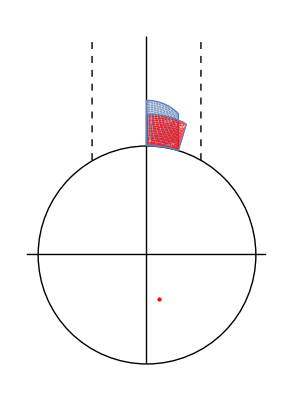

```mathematica
Show[Graphics[Circle[{0,0},1]],
Graphics[Line[{{0,-1},{0,2}}]],
Graphics[Line[{{-1.1,0},{1.1,0}}]],
Graphics[{Dashed,Thick,Line[{{-.5,Sqrt[3]/2},{-.5,2}}]}],
Graphics[{Dashed,Thick,Line[{{.5,Sqrt[3]/2},{.5,2}}]}],
ParametricPlot[{Re[(torusRatio*Exp[I torusAngleFromVectors])],Im[(torusRatio*Exp[I torusAngleFromVectors])]},{α,ArcSin[1-1/(√2)],Pi/4},{β,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-α,(Pi-1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))]))-α},RegionFunction->(1/2 √(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)]+4 √2 √(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)]) Sin[#3] Sin[#3+#4]+8 Sin[#3]^2 Sin[#3+#4]^2)>1 && Tan[#3]< ((-2 √2 Cos[#3+#4] Sin[#3]+√(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)]) Tan[#3+#4])/(√(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)])+2 √2 Sin[#3] Sin[#3+#4])) && (-2 √2 Cos[#3+#4] Sin[#3]+√(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)]) Tan[#3+#4])/(√(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)])+2 √2 Sin[#3] Sin[#3+#4])>0&&
1/(2 √2)Sec[#3] √(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[4 #3+2 #4]+4 Sin[#3] Sin[#3+#4] (√2 √(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[4 #3+2 #4])+2 Sin[#3] Sin[#3+#4]))>1&)],
ParametricPlot[{Re[(1/torusRatio*Exp[I torusAngleFromVectors])],Im[(1/torusRatio*Exp[I torusAngleFromVectors])]},{α,ArcSin[1-1/(√2)],Pi/4},{β,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-α,(Pi-1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))]))-α},RegionFunction->(1/2 √(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)]+4 √2 √(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)]) Sin[#3] Sin[#3+#4]+8 Sin[#3]^2 Sin[#3+#4]^2)>1 && Tan[#3]< ((-2 √2 Cos[#3+#4] Sin[#3]+√(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)]) Tan[#3+#4])/(√(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)])+2 √2 Sin[#3] Sin[#3+#4])) && (-2 √2 Cos[#3+#4] Sin[#3]+√(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)]) Tan[#3+#4])/(√(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)])+2 √2 Sin[#3] Sin[#3+#4])>0&&
1/(2 √2)Sec[#3] √(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[4 #3+2 #4]+4 Sin[#3] Sin[#3+#4] (√2 √(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[4 #3+2 #4])+2 Sin[#3] Sin[#3+#4]))<1&),PlotStyle->Red],
(*Least dense globally maximally dense point*)
Graphics[{Red,Point[{Re[(torusRatio*Exp[I torusAngleFromVectors])],Im[(torusRatio*Exp[I torusAngleFromVectors])]}/.{α->2.4907302,β->2.4907302}]}
]]
```

Note that the red region has been inverted by looking at the torus ratio and determining when it is greater than or less than one.  For example, in the second paramteric plot, notice the last inequality in the RegionFunction corresponds to the torus ratio.  So when this torus ratio is less than one, we take 1/torusratio to flip the region over.

## Density Of Packings

Here we analyze the density of the locally maximally dense packings and explore the density.

```mathematica
torusDensity = FullSimplify[(Pi*(1/2)^2+2*Pi*(1/2(Sqrt[2]-1))^2)/(Norm[latticeVectors[[1]]]*Norm[latticeVectors[[2]]]*Sin[torusAngleFromVectors]) ,{Element[{α,β},Reals],ArcSin[1-1/(√2)]<α<Pi/4,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-α<β<(Pi-1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))]))-α,  1/2 √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]+4 √2 √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]) Sin[α] Sin[α+β]+8 Sin[α]^2 Sin[α+β]^2)>1,Tan[α]<(-2 √2 Cos[α+β] Sin[α]+√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]) Tan[α+β])/(√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)])+2 √2 Sin[α] Sin[α+β]),(-2 √2 Cos[α+β] Sin[α]+√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)]) Tan[α+β])/(√(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[2 (2 α+β)])+2 √2 Sin[α] Sin[α+β])>0}]
```

((7-4 √2) π Csc[α+β] Sec[α])/(4 Cos[β]-4 Cos[2 α+β]+2 √2 √(10-8 √2+2 Cos[2 α]+Cos[2 β]-2 Cos[2 (α+β)]+Cos[4 α+2 β]))

Plot the density over the parameter space

```mathematica
Plot3D[torusDensity,{α,ArcSin[1-1/(√2)],Pi/4},{β,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-α,(Pi-1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))]))-α},RegionFunction->(1/2 √(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)]+4 √2 √(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)]) Sin[#3] Sin[#3+#4]+8 Sin[#3]^2 Sin[#3+#4]^2)>1 && Tan[#3]< ((-2 √2 Cos[#3+#4] Sin[#3]+√(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)]) Tan[#3+#4])/(√(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)])+2 √2 Sin[#3] Sin[#3+#4])) && (-2 √2 Cos[#3+#4] Sin[#3]+√(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)]) Tan[#3+#4])/(√(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)])+2 √2 Sin[#3] Sin[#3+#4])>0&),AxesLabel->Automatic]
```

Plot3D::invregion: (1/2 √(10+Times[«2»]+Times[«2»]+Cos[«1»]+Times[«2»]+Cos[«1»]+Times[«5»]+Times[«3»])>1&&Tan[#3]<(-2 √(«1») Cos[«1»] Sin[«1»]+√(«1») Tan[«1»])/(√(«1»)+Times[«4»])&&(-2 √(«1») Cos[«1»] Sin[«1»]+√(«1») Tan[«1»])/(√(«1»)+Times[«4»])>0&)[Identity[#1],Identity[#2],Identity[#3]]& must be a Boolean function.

-Graphics3D-

Color the moduli space region with color depending on the density. Red shade is close to 1 and Blue shade is close to .5

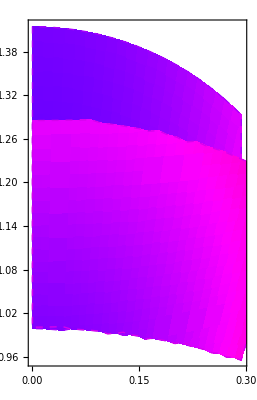

```mathematica
Show[ParametricPlot[{Re[(torusRatio*Exp[I torusAngleFromVectors])],Im[(torusRatio*Exp[I torusAngleFromVectors])]},{α,ArcSin[1-1/(√2)],Pi/4},{β,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-α,(Pi-1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))]))-α},RegionFunction->(1/2 √(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)]+4 √2 √(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)]) Sin[#3] Sin[#3+#4]+8 Sin[#3]^2 Sin[#3+#4]^2)>1 && Tan[#3]< ((-2 √2 Cos[#3+#4] Sin[#3]+√(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)]) Tan[#3+#4])/(√(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)])+2 √2 Sin[#3] Sin[#3+#4])) && (-2 √2 Cos[#3+#4] Sin[#3]+√(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)]) Tan[#3+#4])/(√(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)])+2 √2 Sin[#3] Sin[#3+#4])>0&&
1/(2 √2)Sec[#3] √(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[4 #3+2 #4]+4 Sin[#3] Sin[#3+#4] (√2 √(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[4 #3+2 #4])+2 Sin[#3] Sin[#3+#4]))>1&),ColorFunction->(Hue[torusDensity]/.{α ->#3,β->#4} &),ColorFunctionScaling->False,BoundaryStyle->Directive[Black,Thick,Dashed],Mesh->None] ,
ParametricPlot[{Re[(1/torusRatio*Exp[I torusAngleFromVectors])],Im[(1/torusRatio*Exp[I torusAngleFromVectors])]},{α,ArcSin[1-1/(√2)],Pi/4},{β,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-α,(Pi-1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))]))-α},RegionFunction->(1/2 √(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)]+4 √2 √(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)]) Sin[#3] Sin[#3+#4]+8 Sin[#3]^2 Sin[#3+#4]^2)>1 && Tan[#3]< ((-2 √2 Cos[#3+#4] Sin[#3]+√(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)]) Tan[#3+#4])/(√(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)])+2 √2 Sin[#3] Sin[#3+#4])) && (-2 √2 Cos[#3+#4] Sin[#3]+√(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)]) Tan[#3+#4])/(√(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)])+2 √2 Sin[#3] Sin[#3+#4])>0&&
1/(2 √2)Sec[#3] √(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[4 #3+2 #4]+4 Sin[#3] Sin[#3+#4] (√2 √(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[4 #3+2 #4])+2 Sin[#3] Sin[#3+#4]))<1&),ColorFunction->(Hue[torusDensity]/.{α ->#3,β->#4} &),ColorFunctionScaling->False,BoundaryStyle->Directive[Black,Thick,Dashed],Mesh->None]
]
```

This is the density color as plotted where both sections are above the circle.  Below is the plot where the region hasn’t been flipped over iteself.

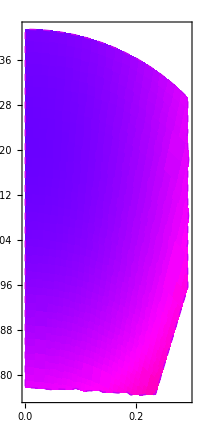

```mathematica
ParametricPlot[{Re[(torusRatio*Exp[I torusAngleFromVectors])],Im[(torusRatio*Exp[I torusAngleFromVectors])]},{α,ArcSin[1-1/(√2)],Pi/4},{β,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-α,(Pi-1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))]))-α},RegionFunction->(1/2 √(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)]+4 √2 √(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)]) Sin[#3] Sin[#3+#4]+8 Sin[#3]^2 Sin[#3+#4]^2)>1 && Tan[#3]< ((-2 √2 Cos[#3+#4] Sin[#3]+√(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)]) Tan[#3+#4])/(√(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)])+2 √2 Sin[#3] Sin[#3+#4])) && (-2 √2 Cos[#3+#4] Sin[#3]+√(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)]) Tan[#3+#4])/(√(10-8 √2+2 Cos[2 #3]+Cos[2 #4]-2 Cos[2 (#3+#4)]+Cos[2 (2 #3+#4)])+2 √2 Sin[#3] Sin[#3+#4])>0&),ColorFunction->(Hue[torusDensity]/.{α ->#3,β->#4} &),ColorFunctionScaling->False,BoundaryStyle->Directive[Black,Thick,Dashed],Mesh->None]
```